Importing data from CERN ROOT files to Mathematica

Ken Hsieh
Technical Staff Member
Wolfram Research Inc

March 8, 2011

```mathematica
$Version
$UserBaseDirectory
```

8.0 for Mac OS X x86 (64-bit) (November 6, 2010)

/Users/yoshi/Library/Mathematica

```mathematica
(* make sure that the necessary converter files are present *)
dir = FileNameJoin[{$UserBaseDirectory, "SystemFiles","Formats","ROOT"}];
FileExistsQ[FileNameJoin[{dir, ReleaseHold[#]}]]&/@{"Import.m","Converter.m",Hold[Sequence["Binaries",$SystemID,"ROOT.exe"]]}
```

{True,True,True}

## ROOT Importer Usage

### File MetaInformation (from TKey Objects)

The wrappers to access TKey functionalities have the form:
  Import[ file, {“ROOT”, “Keys”} ]
or simply as
  Import[ file, “ROOT” ]
and the output has the form:
  { {name1, title1, class1},  {name2, title2, class2}, ... }

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Import["cernstaff.root",{"ROOT","Keys"}]
```

{{T,CERN 1988 staff data,TTree}}

```mathematica
Import["demo.root","ROOT"]
```

{{h0,histo nr:0,TH1F},{h1,histo nr:1,TH1F},{h2,histo nr:2,TH1F},{h3,histo nr:3,TH1F},{h4,histo nr:4,TH1F},{h5,histo nr:5,TH1F},{h6,histo nr:6,TH1F},{h7,histo nr:7,TH1F},{h8,histo nr:8,TH1F},{h9,histo nr:9,TH1F},{h10,histo nr:10,TH1F},{h11,histo nr:11,TH1F},{h12,histo nr:12,TH1F},{h13,histo nr:13,TH1F},{h14,histo nr:14,TH1F}}

```mathematica
Import["th2f.root","ROOT"]
```

{{h2,xygaus + xygaus(5) + xylandau(10),TH2F}}

### Interfaces to TTree Objects

#### Usage Information

The wrappers to access TTree functionalities have the forms:

retrieve metadata (branch names, data types, etc) with “TTreeMetadata”:
  Import[ file, {“ROOT”, “TTreeMetadata”, tree} ]
  
retrieve data from a TTree with “TTreeData”:
  Import[ file, {“ROOT”, “TTreeData”, treet} ],
  Import[ file, {“ROOT”, “TTreeData”, tree, branch} ],
  
use the option “Range” to do a partial import:
  Import[ file, {“ROOT”, “TTreeData”, treet}, “Rage” -> {beg, end } ],
  Import[ file, {“ROOT”, “TTreeData”, tree, branch}, “Range” -> {beg, end } ],

where:
    tree is the name of the TTree object,
    branch is the name of a TBranch object,
    beg  is the starting index (1-indexed) when partially importing a branch,
    end  is the ending index (1-indexed) when partially importing a branch.

Note that, since NTuple inherits from TTree, we can also pass
the name of an NTuple object.

#### Importing the TKey information.

```mathematica
(* This imports the metadata of a given tree *)
Import["cernstaff.root", {"ROOT", "TTreeMetadata", "T"}]
```

{{Category,Category,Int_t,3354},{Flag,Flag,UInt_t,3354},{Age,Age,Int_t,3354},{Service,Service,Int_t,3354},{Children,Children,Int_t,3354},{Grade,Grade,Int_t,3354},{Step,Step,Int_t,3354},{Hrweek,Hrweek,Int_t,3354},{Cost,Cost,Int_t,3354},{Division,Division,Char_t,3354},{Nation,Nation,Char_t,3354}}

```mathematica
(* import the branch information of a TTree *)
header = {"Name","Title","Data Type", "Entries"};
branchinfo=Import["cernstaff.root", {"ROOT", "TTreeMetadata", "T"}];
Grid[Join[ {header}, branchinfo ], Frame-> All]
```

Name | Title | Data Type | Entries
Category | Category | Int_t | 3354
Flag | Flag | UInt_t | 3354
Age | Age | Int_t | 3354
Service | Service | Int_t | 3354
Children | Children | Int_t | 3354
Grade | Grade | Int_t | 3354
Step | Step | Int_t | 3354
Hrweek | Hrweek | Int_t | 3354
Cost | Cost | Int_t | 3354
Division | Division | Char_t | 3354
Nation | Nation | Char_t | 3354

#### Importing one particular branch.

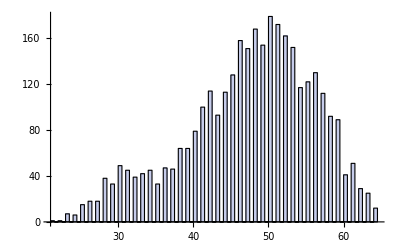

```mathematica
(* This imports the Age branch and plots it as with Histogram[] *)
dat=Import["cernstaff.root", {"ROOT", "TTreeData", "T", "Age"}];
Histogram[dat]
```

#### Importing only parts of one particular branch.

```mathematica
dat=Import["cernstaff.root", {"ROOT", "TTreeData", "T", "Age"}, "Range" -> {11, 20}]
```

Partial branch import with bounds: {11,20}

{51,54,54,46,54,57,55,55,57,51}

#### Importing all branches of a TTree.

```mathematica
(* This imports the metadata and the data a given NTuple *)
Import["basic.root", {"ROOT", "TTreeMetadata", "ntuple"}]
Import["basic.root", {"ROOT", "TTreeData", "ntuple"}]
```

{{x,x,Float_t,4},{y,y,Float_t,4},{z,z,Float_t,4}}

{{-1.,1.,2.,3.5},{2.,5.,5.,3.4},{3.,6.,45.,4.}}

#### Importing only certain parts of all branch of a TTree.

```mathematica
(* We need to use the "Range" option *)
Import["basic.root", {"ROOT", "TTreeData", "ntuple"}, "Range" -> {2,4}]
```

{{1.,2.,3.5},{5.,5.,3.4},{6.,45.,4.}}

#### One more example

```mathematica
(* import only the 11th through 25th entries across all branches *)
alldata=Import["cernstaff.root", {"ROOT", "TTreeData", "T"}, "Range" -> {11,25}];
```

```mathematica
(* present the data visually. *)
header = First/@Import["cernstaff.root", {"ROOT", "TTreeMetadata", "T"}];
Grid[Join[{header}, Transpose[alldata]], Frame->All]
```

Category | Flag | Age | Service | Children | Grade | Step | Hrweek | Cost | Division | Nation
361 | 15 | 51 | 29 | 0 | 7 | 13 | 40 | 7599 | PS | FR
303 | 15 | 54 | 31 | 2 | 8 | 13 | 40 | 9315 | PS | CH
302 | 15 | 54 | 29 | 0 | 7 | 13 | 40 | 7599 | PS | CH
300 | 15 | 46 | 25 | 0 | 8 | 6 | 40 | 7892 | PS | CH
361 | 15 | 54 | 26 | 1 | 7 | 13 | 40 | 7850 | PS | DE
361 | 15 | 57 | 29 | 0 | 7 | 13 | 40 | 7599 | PS | FR
316 | 11 | 55 | 28 | 0 | 8 | 11 | 40 | 8137 | PS | CH
303 | 15 | 55 | 26 | 1 | 7 | 13 | 40 | 7850 | SPS | FR
361 | 15 | 57 | 29 | 1 | 7 | 8 | 40 | 7294 | PS | FR
361 | 15 | 51 | 28 | 2 | 7 | 13 | 40 | 8101 | PS | FR
419 | 13 | 54 | 29 | 0 | 5 | 13 | 40 | 5720 | PS | FR
202 | 15 | 57 | 26 | 1 | 12 | 13 | 40 | 15832 | PS | DE
304 | 15 | 63 | 29 | 1 | 10 | 13 | 40 | 12226 | PS | NL
204 | 15 | 56 | 27 | 0 | 11 | 9 | 40 | 13135 | PS | DE
204 | 15 | 49 | 27 | 0 | 9 | 9 | 40 | 9617 | LEP | GB

Note that the results of 
  Import[ file, {“ROOT”, “TreeData”, tree} ]
is of the form 
  {
    {px1, px2, px3, ...}, //branch px
    {py1, py2, py3, ...}, //branch py
    ...
  }.
To get the first “event”, we would have to Transpose[] the result.
We can easily pick out subportions of the data using the Part[] command of Mathematica.

#### Error handling

```mathematica
(* When the Tree is not present, we exit safely and return $Failed. *)
Import["cernstaff.root", {"ROOT", "TTreeMetadata", "Invalid_Tree"}]
```

No such TTree exists

$Failed

```mathematica
(* When a branch is not present, we exit safely and return $Failed. *)
Import["cernstaff.root", {"ROOT", "TTreeData", "T", "InvalidBranch"}]
```

Allowed TBranches are: {Category,Flag,Age,Service,Children,Grade,Step,Hrweek,Cost,Division,Nation} and InvalidBranch is invalid.

$Failed

```mathematica
(* When the bounds are not appropriate, we exit safely and return $Failed. *)
Import["cernstaff.root", {"ROOT", "TTreeData", "T", "Age"}, "Range" -> {5, 50000000}]
```

Partial branch import with bounds: {5,50000000}

Bound not accessible; the branch Age has only 3354 entires.

$Failed

### Interface with TH1F Object

The wrappers to access TH1F functionalities have the forms:
  Import[ file, {“ROOT”, “TH1FData”, hist} ],
  Import[ file, {“ROOT”, “TH1FGraphics”, hist} ]
where:
    hist  is the name of the TH1F object.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* This imports the histogram data of a given TH1F object. *)
histdata=Import["demo.root",{"ROOT","TH1FData","h7"}];
```

The data is of the form:
  { {x1, Δx1, count1, error1}, {x2, Δx2, count2, error2}, ... }

```mathematica
(* show first 10 entries in a grid *)
head={"x","Δx","count","Δcount"};
Grid[Join[{head},Take[histdata,10]],Frame-> All]
```

x | Δx | count | Δcount
-4. | 0.08 | 0. | 0.
-3.92 | 0.08 | 0. | 0.
-3.84 | 0.08 | 0. | 0.
-3.76 | 0.08 | 0. | 0.
-3.68 | 0.08 | 0. | 0.
-3.6 | 0.08 | 0. | 0.
-3.52 | 0.08 | 0. | 0.
-3.44 | 0.08 | 0. | 0.
-3.36 | 0.08 | 1. | 1.
-3.28 | 0.08 | 0. | 0.

```mathematica
(* Import the histogram directly as a Graphics *)
graphics1=Import["demo.root",{"ROOT","TH1FGraphics","h10"}]
```

Histogram[{0},{{-4.,-3.92,-3.84,-3.76,-3.68,-3.6,-3.52,-3.44,-3.36,-3.28,-3.2,-3.12,-3.04,-2.96,-2.88,-2.8,-2.72,-2.64,-2.56,-2.48,-2.4,-2.32,-2.24,-2.16,-2.08,-2.,-1.92,-1.84,-1.76,-1.68,-1.6,-1.52,-1.44,-1.36,-1.28,-1.2,-1.12,-1.04,-0.96,-0.88,-0.8,-0.72,-0.64,-0.56,-0.48,-0.4,-0.32,-0.24,-0.16,-0.08,0.,0.08,0.16,0.24,0.32,0.4,0.48,0.56,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.36,1.44,1.52,1.6,1.68,1.76,1.84,1.92,2.,2.08,2.16,2.24,2.32,2.4,2.48,2.56,2.64,2.72,2.8,2.88,2.96,3.04,3.12,3.2,3.28,3.36,3.44,3.52,3.6,3.68,3.76,3.84,3.92,4.}},data$52288⟦All,3⟧&]

```mathematica
(* Options available to Histogram[] can be passed directly. *)
graphics2=Import["demo.root",{"ROOT","TH1FGraphics","h7"},ColorFunction->Function[{height},ColorData["Rainbow"][height]]]
```

Histogram[{0},{{-4.,-3.92,-3.84,-3.76,-3.68,-3.6,-3.52,-3.44,-3.36,-3.28,-3.2,-3.12,-3.04,-2.96,-2.88,-2.8,-2.72,-2.64,-2.56,-2.48,-2.4,-2.32,-2.24,-2.16,-2.08,-2.,-1.92,-1.84,-1.76,-1.68,-1.6,-1.52,-1.44,-1.36,-1.28,-1.2,-1.12,-1.04,-0.96,-0.88,-0.8,-0.72,-0.64,-0.56,-0.48,-0.4,-0.32,-0.24,-0.16,-0.08,0.,0.08,0.16,0.24,0.32,0.4,0.48,0.56,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.36,1.44,1.52,1.6,1.68,1.76,1.84,1.92,2.,2.08,2.16,2.24,2.32,2.4,2.48,2.56,2.64,2.72,2.8,2.88,2.96,3.04,3.12,3.2,3.28,3.36,3.44,3.52,3.6,3.68,3.76,3.84,3.92,4.}},data$52338⟦All,3⟧&,ColorFunction→Function[{height},ColorData[Rainbow][height]]]

```mathematica
Show[graphics1]
```

Show::gtype: Histogram is not a type of graphics.

Show[Histogram[{0},{{-4.,-3.92,-3.84,-3.76,-3.68,-3.6,-3.52,-3.44,-3.36,-3.28,-3.2,-3.12,-3.04,-2.96,-2.88,-2.8,-2.72,-2.64,-2.56,-2.48,-2.4,-2.32,-2.24,-2.16,-2.08,-2.,-1.92,-1.84,-1.76,-1.68,-1.6,-1.52,-1.44,-1.36,-1.28,-1.2,-1.12,-1.04,-0.96,-0.88,-0.8,-0.72,-0.64,-0.56,-0.48,-0.4,-0.32,-0.24,-0.16,-0.08,0.,0.08,0.16,0.24,0.32,0.4,0.48,0.56,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.36,1.44,1.52,1.6,1.68,1.76,1.84,1.92,2.,2.08,2.16,2.24,2.32,2.4,2.48,2.56,2.64,2.72,2.8,2.88,2.96,3.04,3.12,3.2,3.28,3.36,3.44,3.52,3.6,3.68,3.76,3.84,3.92,4.}},data$52288⟦All,3⟧&]]

### Interface with TH2F Object

The wrappers to access TH1F functionalities have the forms:
  Import[ file, {“ROOT”, “TH2FData”, hist} ],
  Import[ file, {“ROOT”, “TH2FGraphics”, hist} ]
where:
    hist  is the name of the TH2F object.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* This imports the histogram data of a given TH2F object. *)
data = Import["th2f.root", {"ROOT","TH2FData","h2"}];
```

The data is of the form:
  { {x1, Δx1, count1, error1}, {x2, Δx2, count2, error2}, ... }

```mathematica
(* show first 5 entries in a grid *)
head={"x","Δx","y","Δy","count","Δcount"};
Grid[Join[{head},Take[data,5]],Frame-> All]
```

x | Δx | y | Δy | count | Δcount
-4. | 0.4 | -4. | 0.4 | 1. | 1.
-4. | 0.4 | -3.6 | 0.4 | 11. | 3.31662
-4. | 0.4 | -3.2 | 0.4 | 16. | 4.
-4. | 0.4 | -2.8 | 0.4 | 12. | 3.4641
-4. | 0.4 | -2.4 | 0.4 | 9. | 3.

```mathematica
(* Import the histogram directly as a Graphics *)
graphics3D=Import["th2f.root",{"ROOT","TH2FGraphics","h2"}]
```

Histogram3D[{{0,0}},{{{-4.,-3.6,-3.2,-2.8,-2.4,-2.,-1.6,-1.2,-0.8,-0.4,0.,0.4,0.8,1.2,1.6,2.,2.4,2.8,3.2,3.6,4.}},{{-4.,-3.6,-3.2,-2.8,-2.4,-2.,-1.6,-1.2,-0.8,-0.4,0.,0.4,0.8,1.2,1.6,2.,2.4,2.8,3.2,3.6,4.}}},data$52392&]

```mathematica
(* Options available to Histogram3D[] can be passed directly. *)
graphics=Import["th2f.root",{"ROOT","TH2FGraphics","h2"},ChartElements->Graphics3D@Cuboid[],ChartStyle->"Pastel"]
```